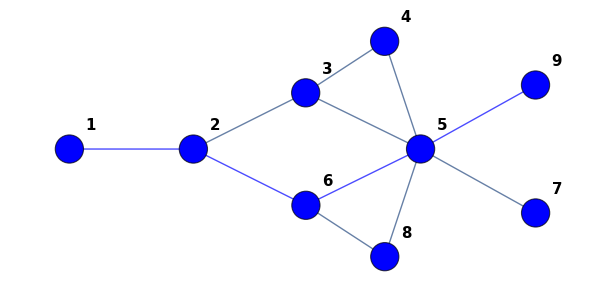

```mathematica
Graph[{3<->5,4<->5,7<->5,3<->2,3<->4,8<->5,8<->6,Style[1<->2,Blue],Style[2<->6,Blue],Style[6<->5,Blue],Style[5<->9,Blue]},VertexStyle->{Blue},VertexSize->0.3,VertexLabels->Table[i->i,{i,9}],VertexLabelStyle->Directive[Black,Bold,15],EdgeStyle->{Black,Thick},EdgeStyle->Opacity[0.5]]
```

```mathematica
Graph[{1<->2,1<->3,1<->4,1<->5,Style[2<->5,White],Style[4<->5,White],Style[3<->4,White],Style[2<->3,White]},VertexStyle->{2->Red,4->Red,3->Red,5->Red,1->Blue},VertexSize->0.3,VertexLabelStyle->Directive[Black,Bold,10],EdgeStyle->{Black,Thick}]
```

-Graphics-

```mathematica
mx=Get["~/Documents/ALEJANDRO/principal/CGigCV/30sMar07.txt"];
```

```mathematica
mx0=Import["~/Documents/ALEJANDRO/principal/retratostxt/10sMar07_retrato.txt","Table"];
```

Import::nffil: File ~/Documents/ALEJANDRO/principal/retratostxt/10sMar07_retrato.txt not found during Import.

```mathematica
ArrayPlot[mx,VertexSize->3]
```

```mathematica
Histogram[mx,20]
```

```mathematica
grafp=AdjacencyGraph[mx,VertexSize->3];
```

```mathematica
CommunityGraphPlot[mx]
```

-Graphics-

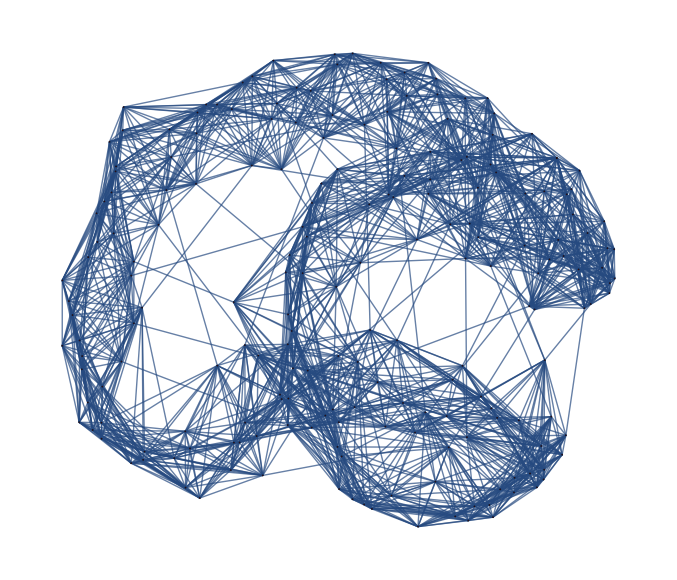

```mathematica
GraphPlot[mx]
```

```mathematica
FindGraphCommunities[AdjacencyGraph[mx],Method->"Modularity"]
```

{{74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73},{201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273}}

```mathematica
Export["~/Documents/ALEJANDRO/principal/comunidades/30sMar07retr.txt",FindGraphCommunities[AdjacencyGraph[mx],Method->"Modularity"]]
```

~/Documents/ALEJANDRO/principal/comunidades/30sMar07retr.txt

```mathematica
464-165
```

299

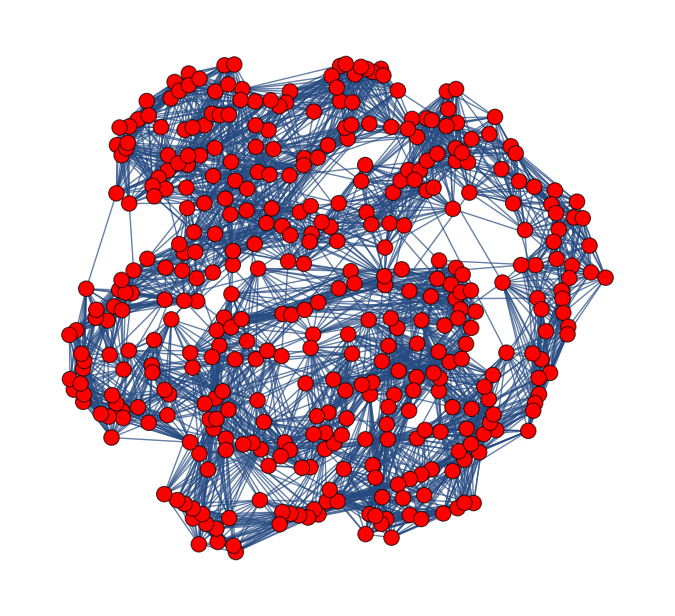

```mathematica
zxmx=RandomGraph[WattsStrogatzGraphDistribution[400,0.02,10],VertexStyle->{Red},VertexSize->3,GraphLayout-> {"SpringEmbedding"}]
```

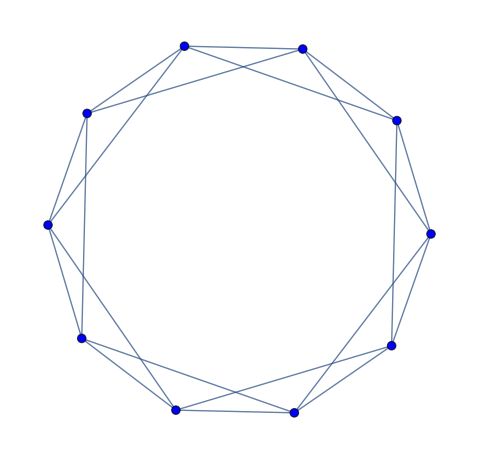

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[10,0.05,2],VertexStyle->{Blue}]
```